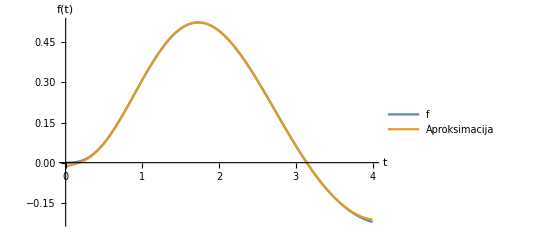

```mathematica
taylor[f_,t_,t0_,stopnja_]:=Module[{vrsta},
vrsta=Normal[Series[f,{t,t0,stopnja}]];

Plot[{f,vrsta},{t,0,4}, PlotLegends->{"f","Aproksimacija"},
AxesLabel->{"t","f(t)"},PlotRange->All]
]

f[t_]= Sin[t] t^2 Exp[-t];
t0=2;

taylor[f[t],t,t0, 10]
```

```mathematica
Manipulate[taylor[f[t],t,t0,stopnja],{{stopnja,6,"Stopnja"},1,10,1},FrameLabel->{"Približek f"}]
```